4 - 10 Orthogonal trajectories (OTs)
Sketch or graph some of the given curves. Guess what their OTs may look like. Find these OTs.

4. y = x^2 +c

```mathematica
Clear["Global`*"]
```

```mathematica
y'=D[C x^2 + c,x]
```

2 C x

```mathematica
ỹ'[x_]=-1/(2 C x)
```

-1/(2 C x)

```mathematica
inter[x_]=∫ỹ'[x]ⅆx
```

-Log[x]/(2 C)

```mathematica
inter[x]=inter[x]+c
```

c-Log[x]/(2 C)

```mathematica
(*tab[x_]=Table[inter[x]/.c->j,{j,-2,2,0.5}/.C->p,{p,1.5}];*)
```

```mathematica
(*ytab[x_]=Table[C x^2+c1/.c1->k,{k,-2,2,0.5}/. C -> r, {r, 1.5}];*)
tab[x_]=Table[inter[x]/.{c->0,C->1}];
tabgr[x_]=Table[inter[x]/.{c->0,C->2}];
```

```mathematica
ytab[x_]=Table[C x^2+c1/.{c1->0, C -> 1}];
ytabgr[x_]=Table[C x^2+c1/.{c1->0, C -> 2}];
```

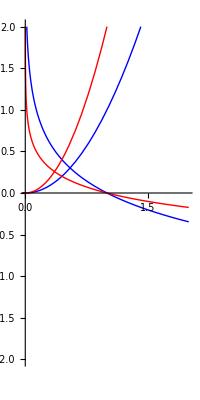

```mathematica
Show[Plot[tab[x],{x, -2,2},PlotRange->{-2,2},PlotStyle->{Blue,Thin},AspectRatio->Automatic],Plot[ytab[x],{x, -2,2},PlotRange->{-2,2},PlotStyle->{Blue,Thin},AspectRatio->Automatic],

Plot[tabgr[x],{x, -2,2},PlotRange->{-2,2},PlotStyle-> {Red,Thin},AspectRatio->Automatic],Plot[ytabgr[x],{x, -2,2},PlotRange->{-2,2},PlotStyle->{Red,Thin},AspectRatio->Automatic]]
```

The integration constant is not meaningful here, the big C, relating to the independent variable, is what makes the orthogonality apparent.

5. y = c x

```mathematica
Clear["Global`*"]
```

```mathematica
y[x_]=c x
```

c x

```mathematica
y'=D[y[x],x]
```

c

```mathematica
ỹ'[x_]=-1/c
```

-1/c

```mathematica
inter[x_]=∫ỹ'[x]ⅆx
```

-x/c

```mathematica
tab[x_]=Table[inter[x]/.c->j,{j,-1,-0.001,1.5}];
```

```mathematica
ytab[x_]=Table[c1 x/.c1->k,{k,-1,0,1.5}];
```

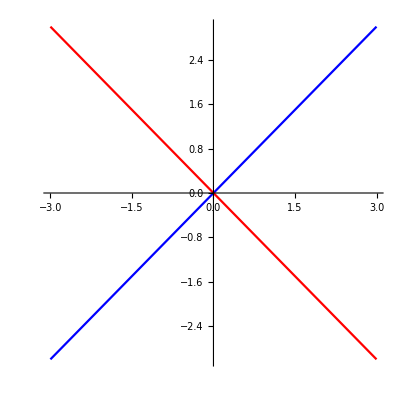

```mathematica
Show[Plot[tab[x],{x, -3,3},PlotRange->{-3,3},PlotStyle->{Blue,Medium},AspectRatio->Automatic],Plot[ytab[x],{x, -3,3},PlotRange->{-3,3},PlotStyle->{Red,Medium},AspectRatio->Automatic]]
```

.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Copyright].07.06.00\[Copyright].07.06\[CapitalADoubleDot]7.81.97.03\[Copyright].07.06.00\[DoubleDot].07.06.00\[Copyright].07.06.00\[Copyright].07.06.98\[CapitalEDoubleDot]\[CapitalAGrave]\[NonBreakingSpace].00.00.00.00.04\[OSlash]\[OHat].03.00.99.9d.01.01.03.00.00.00.00.00.00.00.1c.92.9c.01.01.00.99.9d.01.01.00.80.9c.01.01.00.00.00.02.98C\[YDoubleDot]\[DownQuestion].8808.98.00.99.9d.01.01.03.00.00.00.00\[Copyright].07.06.80\[CapitalEDoubleDot]\[CapitalAGrave]\[NonBreakingSpace]\[Currency]\[CapitalOTilde]\[CapitalAGrave]\[NonBreakingSpace].9f4.81.97.88C\[YDoubleDot]\[DownQuestion]\[CapitalOHat]4.81.97.80\[CapitalEDoubleDot]\[CapitalAGrave]\[NonBreakingSpace]pC\[YDoubleDot]\[DownQuestion].00.00.00.00xC\[YDoubleDot]\[DownQuestion]tC\[YDoubleDot]\[DownQuestion].00.00.00.00.00.80.7f.02.00.02].00.03.00.00.00\[CapitalAGrave].08.00.00.00.00.00.02.00.80.11.020 8.98.00.00.00.02.00.80.11.02.03.00.00.00.00.06.00.00.04.00.00.00.00.99.9d.01.01.00.16.00.00.8a8.98.00.80

6. x y = c

```mathematica
Clear["Global`*"]
```

```mathematica
y[x_]=c/x
```

c/x

```mathematica
y'=D[y[x],x]
```

-c/x^2

```mathematica
ỹ'[x_]=x^2/c
```

x^2/c

```mathematica
inter[x_]:=∫ỹ'[x]ⅆx
```

```mathematica
x^3/(3 c)
(*inter[x] = x^3/(3 c)*)
```

x^3/(3 c)

```mathematica
tab[x_]=inter[x]/.c->.3;
tab2[x_]=inter[x]/.c->.7;
```

```mathematica
ytab[x_]=c/x/.c->.3;
ytab2[x_]=Table[c/x/.c->.7];
```

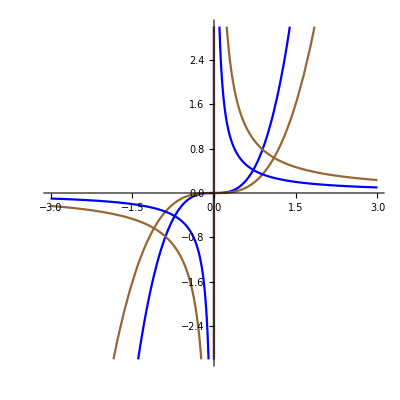

```mathematica
Show[Plot[tab[x],{x, -3,3},PlotRange->{-3,3},PlotStyle->{Blue,Medium},AspectRatio->1/1],Plot[tab2[x],{x, -3,3},PlotRange->{-3,3},PlotStyle->{Brown,Medium},AspectRatio->1/1],Plot[ytab[x],{x, -3,3},PlotRange->{-3,3},PlotStyle->{Blue,Medium},AspectRatio->1/1],
Plot[ytab2[x],{x, -3,3},PlotRange->{-3,3},PlotStyle->{Brown,Medium},AspectRatio->1/1]]
```

.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Copyright].07.06.00\[Copyright].07.06\[CapitalADoubleDot]7.81.97.03\[Copyright].07.06.00\[DoubleDot].07.06.00\[Copyright].07.06.00\[Copyright].07.06.98\[CapitalEDoubleDot]\[CapitalAGrave]\[NonBreakingSpace].00.00.00.00.04\[OSlash]\[OHat].03.00.99.9d.01.01.03.00.00.00.00.00.00.00.1c.92.9c.01.01.00.99.9d.01.01.00.80.9c.01.01.00.00.00.02.98C\[YDoubleDot]\[DownQuestion].8808.98.00.99.9d.01.01.03.00.00.00.00\[Copyright].07.06.80\[CapitalEDoubleDot]\[CapitalAGrave]\[NonBreakingSpace]\[Currency]\[CapitalOTilde]\[CapitalAGrave]\[NonBreakingSpace].9f4.81.97.88C\[YDoubleDot]\[DownQuestion]\[CapitalOHat]4.81.97.80\[CapitalEDoubleDot]\[CapitalAGrave]\[NonBreakingSpace]pC\[YDoubleDot]\[DownQuestion].00.00.00.00xC\[YDoubleDot]\[DownQuestion]tC\[YDoubleDot]\[DownQuestion].00.00.00.00.00.80.7f.02.00.02].00.03.00.00.00\[CapitalAGrave].08.00.00.00.00.00.02.00.80.11

7. y = c/x^2

```mathematica
Clear["Global`*"]
```

```mathematica
y[x_]=c/x^2
```

c/x^2

```mathematica
y'=D[y[x],x]
```

-(2 c)/x^3

```mathematica
ỹ'[x_]=x^3/(2 c)
```

x^3/(2 c)

```mathematica
inter[x_]=∫ỹ'[x]ⅆx
```

x^4/(8 c)

```mathematica
tab[x_]=inter[x]/.c->1;
```

```mathematica
tab2[x_]=inter[x]/.c->2;
```

```mathematica
ytab[x_]=c/x^2/.c->1;
ytab2[x_]=c/x^2/.c->2;
```

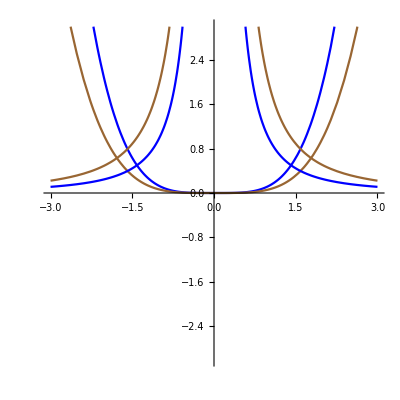

```mathematica
Show[Plot[tab[x],{x, -3,3},PlotRange->{-3,3},PlotStyle->{Blue,Medium},AspectRatio->1/1],Plot[tab2[x],{x, -3,3},PlotRange->{-3,3},PlotStyle->{Brown,Medium},AspectRatio->1/1],Plot[ytab[x],{x, -3,3},PlotRange->{-3,3},PlotStyle->{Blue,Medium},AspectRatio->1/1],
Plot[ytab2[x],{x, -3,3},PlotRange->{-3,3},PlotStyle->{Brown,Medium},AspectRatio->1/1]]
```

8. y=√(x+c)

```mathematica
Clear["Global`*"]
```

```mathematica
y[x_]:=√(C x+c)
```

```mathematica
D[y[x],x]
```

C/(2 √(c+C x))

```mathematica
ỹ'[x_]:=(-2 √(c+C x))/C
```

```mathematica
(*inter[x_]:=∫ỹ'[x]ⅆx*)
```

```mathematica
Integrate[ỹ'[x],x]
```

-(4 (c+C x)^(3/2))/(3 C^2)

```mathematica
thisx[x_]:=-(4 (c+C x)^(3/2))/(3 C^2)
```

```mathematica
thisx1[x_]=thisx[x]/.{c->-1.5,C->-.5}
```

-5.33333 (-1.5-0.5 x)^(3/2)

```mathematica
thisx2[x_]:=thisx[x]/.{c->1.5,C->.5}
```

```mathematica
thisx2[1]
```

-15.0849

```mathematica
ytab[x_]:=√(C x+c)/.{c->1.5,C->.5};


ytabm[x_]=-√(C x+c)/.{c->1.5,C->.5};
ytabm[-1]
```

-1.

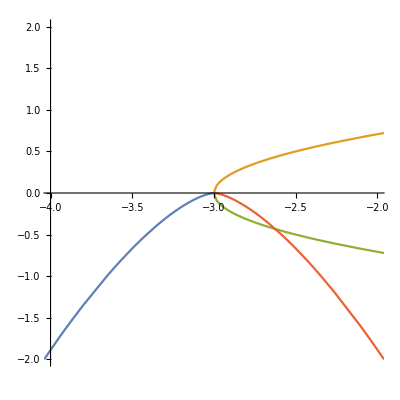

```mathematica
Plot[{thisx1[x],ytab[x],ytabm[x],thisx2[x]},{x,-30,30},PlotRange->{{-4,-2},{-2,2}}, AspectRatio->1/1,GridLines->All]
```

To me, it looks like these display orthogonality, in pairs.

9. y = ce^(-x^2)

```mathematica
Clear["Global`*"]
```

```mathematica
y[x_]:=c ⅇ^(-C x^2)
```

```mathematica
D[y[x],x]
```

-2 c C ⅇ^(-C x^2) x

```mathematica
ỹ'[x_]:=1/(2 c C x ⅇ^(-C x^2))
```

```mathematica
(*inter:=∫ỹ'[x]ⅆx*)
```

```mathematica
Integrate[ỹ'[x],x]
```

ExpIntegralEi[C x^2]/(4 c C)

```mathematica
perx[x_]:= ExpIntegralEi[C x^2]/(4 c C)
```

```mathematica
tab[x_]:=perx[x]/.{c->1,C->1.5};
tab2[x_]:=Table[inter/.c->o,{o,0.001,2,.5}];
```

```mathematica
ytab[x_]:=c ⅇ^(-C x^2)/.{c->1,C->1.5};
```

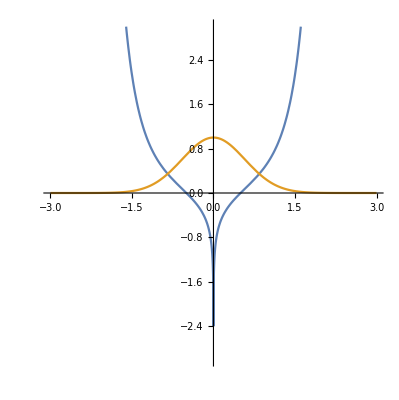

```mathematica
Plot[{tab[x],ytab[x]},{x,-3,3},PlotRange->{-3,3}, AspectRatio-> Automatic,GridLines->Full]
```

.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Copyright].07.06.00\[Copyright].07.06\[CapitalADoubleDot]7.81.97.03\[Copyright].07.06.00\[DoubleDot].07.06.00\[Copyright].07.06.00\[Copyright].07.06.98

.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Copyright].07.06.00\[Copyright].07.06\[CapitalADoubleDot]7.81.97.03\[Copyright].07.06.00\[DoubleDot].07.06.00\[Copyright].07.06.00\[Copyright].07.06.98\[CapitalEDoubleDot]\[CapitalAGrave]\[NonBreakingSpace].00.00.00.00.04\[OSlash]\[OHat].03.00.99.9d.01.01.03.00.00.00.00.00.00.00.1c.92.9c.01.01.00.99.9d.01.01.00.80.9c.01.01.00.00.00.02.98C\[YDoubleDot]\[DownQuestion].8808.98.00.99.9d.01.01.03.00.00.00.00\[Copyright].07.06.80\[CapitalEDoubleDot]\[CapitalAGrave]\[NonBreakingSpace]\[Currency]\[CapitalOTilde]\[CapitalAGrave]\[NonBreakingSpace].9f4.81.97.88C\[YDoubleDot]\[DownQuestion]\[CapitalOHat]4.81.97.80\[CapitalEDoubleDot]\[CapitalAGrave]\[NonBreakingSpace]pC\[YDoubleDot]\[DownQuestion].00.00.00.00xC\[YDoubleDot]\[DownQuestion]tC\[YDoubleDot]\[DownQuestion].00.00.00.00.00.80.7f.02.00.02].00.03.00.00.00\[CapitalAGrave].08.00.00.00.00.00.02.00.80.11.020 8.98.00.00.00.02.00.80.11.02.03.00.00.00.00.06.00.00.04.00.00.00.00.99.9d.01.01.00.16.00.00.8a8.98.00.80.9c.01.01\[CapitalOSlash]C\[YDoubleDot]\[DownQuestion]\[Copyright].1c8.98.00.80.9c.01.01.00TC.02.00.16.00.00\[UGrave]P(.00\[CapitalEth])\[ADoubleDot]
.00\[CapitalEHat](.02\[CapitalOSlash]C\[YDoubleDot]\[DownQuestion]\[EAcute].00&.00.00\[CapitalEHat](.02.9e.00.00.00&.01.01\[NonBreakingSpace]\[ARing].00TC.028.90\[CapitalAGrave]\[NonBreakingSpace].01.01.00.00.00.08E\[YDoubleDot]\[DownQuestion]\[CapitalATilde]Af.00.00TC.02h(.01.01.00H\[CapitalIGrave]\[CapitalAGrave]\[NonBreakingSpace].00.00.00.00.03.02.00.00.00.00.00.00.00.02.00.004\[CapitalIGrave]\[CapitalAGrave]\[NonBreakingSpace].00.00.00.00.9f4.81.97.04.00.00.01.01.16GT.00.00.00.00.00@D\[YDoubleDot]\[DownQuestion].04.00.00.01.01\[Currency].81.01.01.00.16GT.00.00.00.00.00\[OTilde].01.01.00.00.14.00.00.00.00.00.00.00.8d\[CCedilla]\[CapitalUGrave]V.00.00.00.00.8d\[CCedilla]\[CapitalUGrave]V.00.00.00.00.8d\[CCedilla]\[CapitalUGrave]V.00.00.00.00.8d\[CCedilla]\[CapitalUGrave]V.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.10.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.14.06Z.02\[DoubleDot]D\[YDoubleDot]\[DownQuestion]\[AAcute].(.00\[AGrave]PN.04.14.06Z.02.00.00.00.00.00.06Z.02HE\[YDoubleDot]\[DownQuestion]

10. x^2 + (y-c)^2=c^2

```mathematica
Clear["Global`*"]
```

```mathematica
Solve[C x^2+(y-c)^2==c^2,y]
```

{{y→c-√(c^2-C x^2)},{y→c+√(c^2-C x^2)}}

.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00.00\[Copyright].07.06.00\[Copyright].07.06\[CapitalADoubleDot]7.81.97.03\[Copyright].07.06.00\[DoubleDot].07.06.00\[Copyright].07.06.00\[Copyright].07.06.98\[CapitalEDoubleDot]\[CapitalAGrave]\[NonBreakingSpace].00.00.00.00.04\[OSlash]\[OHat].03.00.99.9d.01.01.03.00.00.00.00.00.00.00.1c.92.9c.01.01.00.99.9d.01.01.00.80.9c.01.01.00.00.00.02.98C\[YDoubleDot]\[DownQuestion].8808.98.00.99

```mathematica
y[x_]:=c+√(c^2-C x^2)
```

```mathematica
D[y[x],x]
```

-(C x)/(√(c^2-C x^2))

```mathematica
ỹ'[x_]:=(√(c^2-C x^2))/(C x)
```

```mathematica
(*inter=∫ỹ'[x]ⅆx*)
```

```mathematica
Integrate[ỹ'[x],x]
```

(√(c^2-C x^2)+c Log[x]-c Log[c^2+c √(c^2-C x^2)])/C

```mathematica
cras[x_]:=(√(c^2-C x^2)+c Log[x]-c Log[c^2+c √(c^2-C x^2)])/C
```

```mathematica
fab[x_]:=cras[x]/.{c->.2,C->1};
faby[x_]:=y[x]/.{c->.2,C->1};
fab2[x_]:=cras[x]/.{c->-.2,C->-3};
```

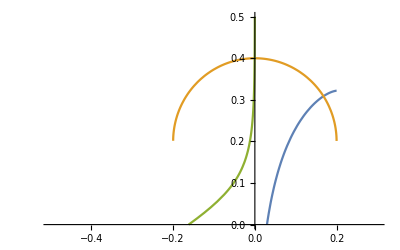

```mathematica
Plot[{fab[x],faby[x],fab2[x]},{x,-0.5,.3},PlotRange->{{-0.5,.3},{0,0.5}},AspectRatio->Automatic]
```

For this one, the third curve (green) is just ad hoc.